```mathematica
Limit[(1+Log[x]/n)^n,{n->Infinity}]
```

{x}

```mathematica
K[n_,0]:=K[n,0]=If[n==1,1,0]
K[n_,1]:=K[n,1]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K[n_,k_]:=K[n,k]=Sum[K[j,k-1]K[n/j,1],{j,Divisors[n]}]
```

```mathematica
K2[n_ ] := K2[n]= Sum[ (-1)^(k+1)/k K[n,k],{k,1,Log[2,n]}]
PK2[n_,0]:=PK2[n,0]=1
PK2[n_,1] := PK2[n,1]=Sum[ K2[j],{j,2,n}]
PK2[n_,k_] := PK2[n,k]=Sum[ K2[j]PK2[Floor[n/j],k-1],{j,2,n}]
```

```mathematica
Table[PK2[n,1],{n,2,100}]
```

{1,2,2,3,2,3,19/6,19/6,13/6,19/6,11/3,14/3,11/3,8/3,65/24,89/24,101/24,125/24,137/24,113/24,89/24,113/24,35/8,35/8,27/8,85/24,97/24,121/24,169/24,193/24,973/120,853/120,733/120,613/120,523/120,643/120,523/120,403/120,121/40,161/40,241/40,281/40,301/40,321/40,281/40,321/40,983/120,983/120,1043/120,923/120,983/120,1103/120,1063/120,943/120,301/40,261/40,221/40,261/40,181/40,221/40,181/40,201/40,911/180,731/180,1091/180,1271/180,1361/180,1181/180,1541/180,1721/180,1841/180,2021/180,1841/180,1931/180,2021/180,1841/180,2201/180,2381/180,2411/180,4837/360,4477/360,4837/360,4117/360,3757/360,3397/360,3037/360,2917/360,3277/360,2557/360,2197/360,2377/360,2017/360,1657/360,1297/360,251/72,323/72,359/72,395/72,341/72}

```mathematica
PA[n_, a_] := Sum[ a^k/k! PK2[n,k],{k,0,Log[2,n]}]
```

```mathematica
PA[100,1]-1
```

428/15

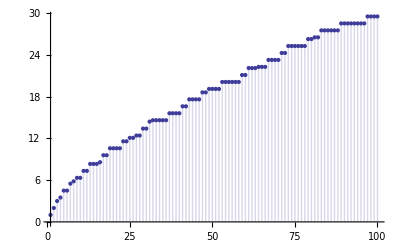

```mathematica
DiscretePlot[ PA[n,1],{n,1,100}]
```

```mathematica
DiscretePlot[ PA[n,1],{n,1,100}]
```

-Graphics-